```mathematica
V=1.75;
R=50.8;
c=0.000001;
L=0.474;
```

```mathematica
function[omega_]=(2*V*R)/Sqrt[(231+R)^2 + ((omega*L)-(1/(omega*c)))^2]
```

177.8/(√(79411.2+(-(1.×10^6)/omega+0.474 omega)^2))

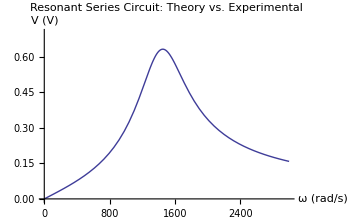

```mathematica
plot1=Plot[function[omega],{omega,0,3000}, PlotRange-> {0,0.7},AxesLabel->{"ω (rad/s)","V (V)"},PlotLabel->"Resonant Series Circuit: 
Theory vs. Experimental"]
```

```mathematica
list=Import["~/summer-work/physics397-FA2013/RLC-Resonant-Circuits/companion-guide/RLC-Resonant-Circuits-Series-Data-Mathematica.csv"];
```

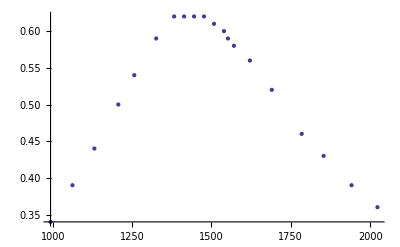

```mathematica
plot2=ListPlot[Table[{list[[i,1]],list[[i,3]]},{i,1,20}]]
```

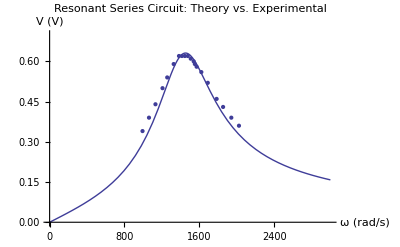

```mathematica
Show[plot1,plot2]
```